Let us consider two vector fields:

```mathematica
X = {x y ,x^2};
Y = {0,y};
```

Here the standard basis vector fields are ∂/∂x and ∂/∂y

let us plot these vector fields:

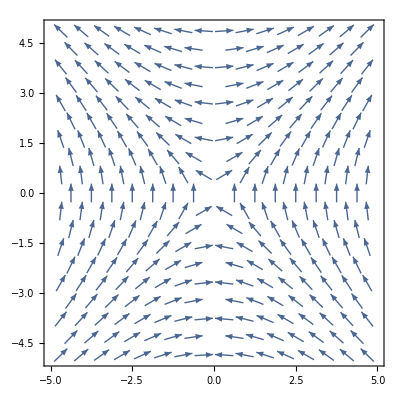
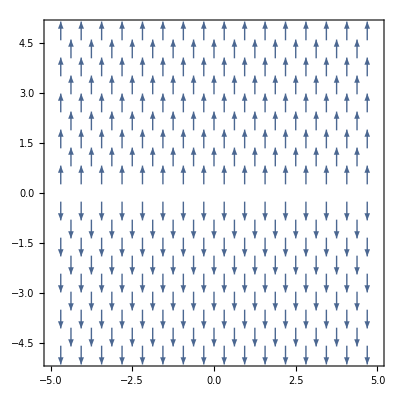

```mathematica
VectorPlot[#,{x,-5,5},{y,-5,5},VectorColorFunction->None]&/@{X,Y}
```

We consider vectors at a particular point, say (1,1)

```mathematica
p={1,1};
{Xp,Yp} ={ X,Y}/.MapThread[Rule,{{x,y},p}];
```

The vector Xp is denoted in red and Yp is denoted in blue color.

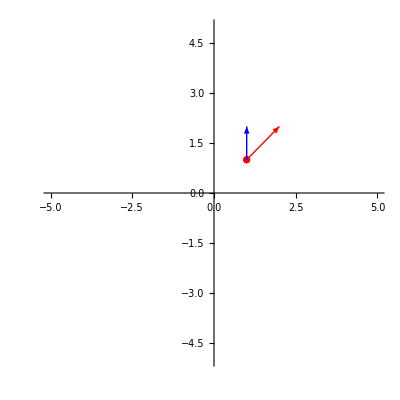

```mathematica
Show[ListPlot[{p},PlotRange->{{-5,5},{-5,5}},PlotStyle->Red],
Graphics[{Red,Arrow[{p,p+Xp}]},PlotRange->{{-5,5},{-5,5}}],
Graphics[{Blue,Arrow[{p,p+Yp}]},PlotRange->{{-5,5},{-5,5}}],AspectRatio-> 1]
```

Now consider a map f:R^2 -> R^2 given by

```mathematica
f[{x_,y_}] ={ x+ y,x- y};
```

The point P gets mapped to fp

```mathematica
fp = f[p]
```

{2,0}

Let us see how the vectors Xp and Yp are pushed forward by this map.

```mathematica
XXp = Xp*Table[D[i,j],{i,f[{x,y}]},{j,{x,y}}]/.MapThread[Rule,{{x,y},p}]//Total
YYp = Yp*Table[D[i,j],{i,f[{x,y}]},{j,{x,y}}]/.MapThread[Rule,{{x,y},p}]//Total
```

{2,0}

{1,-1}

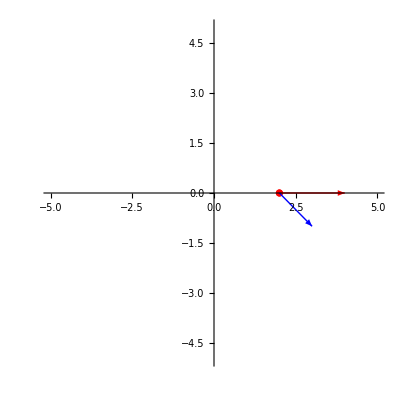

```mathematica
Show[ListPlot[{fp},PlotRange->{{-5,5},{-5,5}},PlotStyle->Red],
Graphics[{Red,Arrow[{fp,fp+XXp}]},PlotRange->{{-5,5},{-5,5}}],
Graphics[{Blue,Arrow[{fp,fp+YYp}]},PlotRange->{{-5,5},{-5,5}}],AspectRatio-> 1]
```